```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation["fish", All]];
```

```mathematica
rawTranslations
```

{Mandarin Chinese→魚,Hindi→मछली,Spanish→pez,Russian→рыба,Indonesian→ikan,Portuguese→peixe,Bengali→মাছ,Arabic→سَمَكَة,Malay→ikan,Japanese→喉,French→poisson,German→Fisch,Urdu→مچهلی,Javanese→iwak,Turkish→balık,Telugu→చేప,Marathi→मासा,Vietnamese→cá,Korean→물고기,Tamil→மீன்,Thai→ปลา,Italian→pesce,Yue Chinese→鱼,Swahili→samaki,Northern Pashto→ټپ,Gujarati→માછલી,Polish→ryba,Ukrainian→риба,Hausa→kifi,Xiang Chinese→yu,Malayalam→മത്സം,Kannada→ಮೀನು,Burmese→ငါး,Oriya→ମାଛ,Hakka Chinese→魚,Panjabi→مچهی,Sundanese→lauk,Bhojpuri→मछरी,Maithili→माछ,South Azerbaijani→balıq,Romanian→peşte,Tagalog→isda,Dutch→vis,Sindhi→مڇي,Cebuano→isda,Igbo→azu,Amharic→ዓሣ,Nepali→माछा,Assamese→মাছ,Hungarian→hal,Madurese→juko',Khmer→រតី,Marwari→मछळी,Adamawa Fulfulde→liingu,Magahi→मछली,Somali→kalluun,Modern Greek→ψάρι,Serbian→riba,Czech→ryba,Shona→hove,Dari→ماهی,Qiubei Zhuang→bla,Zulu→inhlazi,Nyanja→nsomba,Lombard→pes,Belarusian→рыба,Bulgarian→риба,Swedish→fisk,Akan→nsuo mu nam,Kazakh→балық,Iloko→lames,Uighur→белиқ,Kinyarwanda→Jcinyanja,Xhosa→intlanzi,Hiligaynon→isda,Lingala→mbisi,Armenian→ձուկ,Catalan→peix,Tatar→балык,Minangkabau→lauk,Turkmen→balyk,Croatian→riba,Santali→हाकु,Afrikaans→vis,Danish→fisk,Kikuyu→thamaki,Finnish→kala,Hebrew→דג,Slovak→ryba,Eastern Balochi→ماهي، ماهيگ,Rundi→ifi,Norwegian→fisk,Kashmiri→गाड,Tibetan→ཉ་,Tswana→tlhapi,Basque→arrain,Georgian→თევზი,Pedi→hlapi,Wolof→jën,Central Bikol→sira,Buginese→bale,Tsonga→hlampfi,Galician→peixe,Eastern Yiddish→פיש,Kirghiz→балык,Lithuanian→žuvis,Achinese→eungkot,Kalenjin→njiriot,Zarma→hamisa,Esperanto→fiŝo,Slovenian→riba,Sidamo→qilxi'me,Bashkir→балыҡ,Chuvash→пулӑ,Swati→inhlanti,Makasar→juku,Macedonian→риба,Gusii→enswe,North Ndebele→ihlambi,Latvian→zivs,Tonga→ika,Tumbuka→somba,Teso→ekoleit,Newari→यां,Breton→pesk,Estonian→kala,Scots→iasg,Venda→khovhe,Chechen→чІара,Mapudungun→challwa,Ayacucho Quechua→challwa,Masai→sinkir,Erzya→кал,Krio→pwason,Fang→kuas,Kusaal→zīη,Kara-Kalpak→balıq,Sango→susu,Efik→iyak,Aklanon→isda,Maltese→ħuta,Yakut→балык,Samoan→i'a,Missing[NotAvailable]→pouissoun,Komi-Zyrian→чери,Fijian→ika,Icelandic→fiskur,Papiamento→piská,Moksha→кал,Kumyk→балыкъ,Navajo→łóó',Maori→ika,Gagauz→balık,Central Kaqchikel→kär,Dungan→йү,Kashubian→rëba,Kaba→kandje,Khakas→палых,Akaselem→ikuyu,Faroese→fiskur,Ga'anda→ekyenyanja,Romansch→pesch,Evenki→олло,Chorti→chay,Khanty→хуӆ,Chukot→ыннээн,Sanskrit→मीन,Chiripá→pira,Nanai→согдата,Choctaw→nani,Mansi→хул,Koryak→ынныын,Ho-Chunk→hóra,Karaim→балыкъ,Karon Dori→кол,Bai→sumuti,Batak→dekke,Gilyak→ч’о,Alabama→ɬaɬo,Judeo-Crimean Tatar→балых,Latin→piscis,Classical Quechua→challwa}

```mathematica
translatedList = Transliterate[Values[rawTranslations]]
```

{yu,machali,pez,ryba,ikan,peixe,macha,samakat,ikan,hou,poisson,Fisch,mchhly,iwak,balik,cepa,masa,ca,mulgogi,min,pla,pesce,yu,samaki,ټp,machali,ryba,riba,kifi,yu,matsam,minu,ငါး,macha,yu,mchhy,lauk,machari,macha,baliq,peste,isda,vis,mڇy,isda,azu,ዓሣ,macha,macha,hal,juko',រតី,machali,liingu,machali,kalluun,psari,riba,ryba,hove,mahy,bla,inhlazi,nsomba,pes,ryba,riba,fisk,nsuo mu nam,balykˌ,lames,belikˌ,Jcinyanja,intlanzi,isda,mbisi,juk,peix,balyk,lauk,balyk,riba,haku,vis,fisk,thamaki,kala,dg,ryba,mahy, mahyg,ifi,fisk,gada,ཉ་,tlhapi,arrain,tevzi,hlapi,jen,sira,bale,hlampfi,peixe,pys,balyk,zuvis,eungkot,njiriot,hamisa,fiso,riba,qilxi'me,balyҡ,pula,inhlanti,juku,riba,enswe,ihlambi,zivs,ika,somba,ekoleit,yam,pesk,kala,iasg,khovhe,cIara,challwa,challwa,sinkir,kal,pwason,kuas,zie,baliq,susu,iyak,isda,huta,balyk,i'a,pouissoun,ceri,ika,fiskur,piska,kal,balyk",loo',ika,balik,kar,jү,reba,kandje,palyh,ikuyu,fiskur,ekyenyanja,pesch,ollo,chay,huӆ,ynneen,mina,pira,sogdata,nani,hul,ynnyyn,hora,balyk",kol,sumuti,dekke,c'o,lalo,balyh,piscis,challwa}

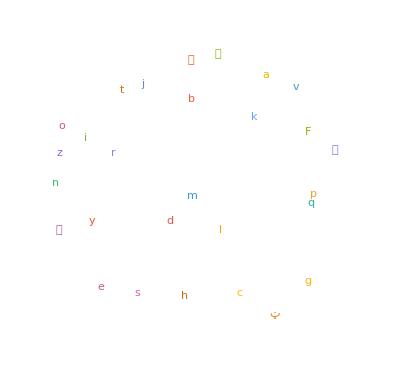

```mathematica
WordCloud[StringTake[translatedList, 1]]
```

```mathematica
audioSpanish=SpeechSynthesize[WordTranslation["fish", "Spanish"][[2]]]
```

```mathematica
audioFrench=SpeechSynthesize[WordTranslation["fish", "French"][[1]]]
```

```mathematica
Spectrogram[audioSpanish]
```

-Graphics-

```mathematica
Spectrogram[audioFrench]
```

-Graphics-

```mathematica
ss=SpectrogramArray[audioSpanish]
```

```mathematica
sf=SpectrogramArray[audioFrench]
```